# Writing Songs in Mathematica

## A Beginner's Guide

Written by Traci Johnson
Last Update: July 28, 2010

## Introduction

The name of this notebook should really be "how to be a total nerd," but I'll be kind. If don't mind sacrificing any reputations you may have amongst people who've never opened up a Mathematica notebook in their entire lives for gaining "street kred" amongst other science and math geeks, then by all means, continue.

Ok, so you want to learn how to write songs in Mathematica? Well, it takes quite a bit of skill. Those of you well-versed in Mathematica coding or programming in general should be able to pick this up quite quickly. However, songwriting is also an art and requires a bit of knowledge about music as well. So if you're tone deaf or can't keep a beat to save your life then this may end up being quite a challenge for you.

So, here's how it's gonna go. I'll start by explaining the two Mathematica functions you will be learning and the syntax needed to get all your instruments to play properly. Then I'll walk you through the steps of creating a "logical" sequence of notes that you can develop into a lengthy song. Then, I'll give you some hints for troubleshooting and some tools that are helpful for successfully composing/arranging your music.

Note: I do assume the reader has some experience with Mathematica and has used it's many other functions in the past. If you've never used Mathematica before, you probably shouldn't start here. Go to a more general Mathematica tutorial first and comeback when you know how to plot things and such.

## The Sound[] and SoundNote[] Functions

K, so there are like, two functions in Mathematica you're going to need to know before you get started. Sound[] is a Mathematica function that takes a certain mathematical function and plays it as an audio track. For example, if I wanted to hear what a pair of sine waves sound like together, I could type in this:

```mathematica
Sound[{Play[Sin[1000t(1+t^2)],{t,0,.2}],Play[Sin[500t (1+t^3)],{t,0,.5}]}]
```

-Graphics-

And "poof," magic! You've turned math into sound! So now, we can instead play something more interesting, like actual musical notes. SoundNote[] does just that. It tells the Sound[] function to play a note from a certain instrument. Wanna hear Sierpinski's Triangle played on piano?

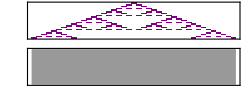

```mathematica
Sound[SoundNote[DeleteCases[3 Range[21]Reverse[#],0]-24,.1]&/@Transpose[CellularAutomaton[90,{{1},0},20]]]
```

So, yes, you can create music out of math. Now we will learn how to string together notes in a less logical and more symphonic series.

## SoundNote[] Syntax

### Syntax

For instruments that make musical tones, you need to use this syntax with SoundNote[]:

```mathematica
SoundNote["pitch",{initaltime,finaltime},"instrument",SoundVolume->v]
```

For percussion instruments, you need to use this syntax with SoundNote[]:

```mathematica
SoundNote["instrument",{initaltime,finaltime},SoundVolume->v]
```

This is how you should write up your code:

```mathematica
Sound[{SoundNote[note1],SoundNote[note2],...,SoundNote[noteN]}]
```

Don't forget the curly brackets around notes! You can place carriage returns and spaces anywhere you want in your song and not mess up the code! I suggest only placing these after the notes, though.

### Parameters

#### Pitch

A string - you need to specify the letter of the pitch (A-G) and which octave it lies in - middle C is C4. Mathematica recognizes accidentals too - sharp is pound sign and flat is lower case B (I'm sure there's something for natural, but I don't know why you would ever need it in this case). So an A major scale above middle C would be:

```mathematica
"A4","B4","C#5","D5","E5","F#5","G#5","A5"
```

And a D minor scale below middle C would be:

```mathematica
"D3","Eb3","Fb3","G3","A3","Bb3","C4","D4"
```

#### Time

Just plain old numbers. Mathematica uses seconds as its unit of time. Specify when you want the note to start playing and when you want it to end in curly brackets separated by a comma. You can actually switch these values around and it will still work, I think (this can be good or bad).

#### Instrument

Choose from a collection of instruments provided by Mathematica. Just type in the string - obviously spelling counts, but less obvious is that these strings are case sensitive! Here's the list of melodic instruments:

"Accordion" | "Agogo" | "AltoSax" | "Applause"
"Atmosphere" | "Bagpipe" | "Bandoneon" | "Banjo"
"BaritoneSax" | "Bass" | "BassAndLead" | "Bassoon"
"Bird" | "BlownBottle" | "Bowed" | "BrassSection"
"Breath" | "Brightness" | "BrightPiano" | "Calliope"
"Celesta" | "Cello" | "Charang" | "Chiff"
"Choir" | "Clarinet" | "Clavi" | "Contrabass"
"Crystal" | "DrawbarOrgan" | "Dulcimer" | "Echoes"
"ElectricBass" | "ElectricGrandPiano" | "ElectricGuitar" | "ElectricPiano"
"ElectricPiano2" | "EnglishHorn" | "Fiddle" | "Fifths"
"Flute" | "FrenchHorn" | "FretlessBass" | "FretNoise"
"Glockenspiel" | "Goblins" | "Guitar" | "GuitarDistorted"
"GuitarHarmonics" | "GuitarMuted" | "GuitarOverdriven" | "Gunshot"
"Halo" | "Harmonica" | "Harp" | "Harpsichord"
"Helicopter" | "HonkyTonkPiano" | "JazzGuitar" | "Kalimba"
"Koto" | "Marimba" | "MelodicTom" | "Metallic"
"MusicBox" | "MutedTrumpet" | "NewAge" | "Oboe"
"Ocarina" | "OrchestraHit" | "Organ" | "PanFlute"
"PercussiveOrgan" | "Piano" | "Piccolo" | "PickedBass"
"PizzicatoStrings" | "Polysynth" | "Rain" | "Recorder"
"ReedOrgan" | "ReverseCymbal" | "RockOrgan" | "Sawtooth"
"SciFi" | "Seashore" | "Shakuhachi" | "Shamisen"
"Shanai" | "Sitar" | "SlapBass" | "SlapBass2"
"SopranoSax" | "Soundtrack" | "Square" | "Steeldrums"
"SteelGuitar" | "Strings" | "Strings2" | "Sweep"
"SynthBass" | "SynthBass2" | "SynthBrass" | "SynthBrass2"
"SynthDrum" | "SynthStrings" | "SynthStrings2" | "SynthVoice"
"Taiko" | "Telephone" | "TenorSax" | "Timpani"
"Tinklebell" | "TremoloStrings" | "Trombone" | "Trumpet"
"Tuba" | "TubularBells" | "Vibraphone" | "Viola"
"Violin" | "Voice" | "VoiceAahs" | "VoiceOohs"
"Warm" | "Whistle" | "Woodblock" | "Xylophone"

And the list of percussion instruments:

"BassDrum" | "BassDrum2" | "BellTree" | "Cabasa"
"Castanets" | "ChineseCymbal" | "Clap" | "Claves"
"Cowbell" | "CrashCymbal" | "CrashCymbal2" | "ElectricSnare"
"GuiroLong" | "GuiroShort" | "HighAgogo" | "HighBongo"
"HighCongaMute" | "HighCongaOpen" | "HighFloorTom" | "HighTimbale"
"HighTom" | "HighWoodblock" | "HiHatClosed" | "HiHatOpen"
"HiHatPedal" | "JingleBell" | "LowAgogo" | "LowBongo"
"LowConga" | "LowFloorTom" | "LowTimbale" | "LowTom"
"LowWoodblock" | "Maracas" | "MetronomeBell" | "MetronomeClick"
"MidTom" | "MidTom2" | "MuteCuica" | "MuteSurdo"
"MuteTriangle" | "OpenCuica" | "OpenSurdo" | "OpenTriangle"
"RideBell" | "RideCymbal" | "RideCymbal2" | "ScratchPull"
"ScratchPush" | "Shaker" | "SideStick" | "Slap"
"Snare" | "SplashCymbal" | "SquareClick" | "Sticks"
"Tambourine" | "Vibraslap" | "WhistleLong" | "WhistleShort"

Also, if you know MIDI instruments, Mathematica recognizes those too. More information can be found on the SoundNote[] help page.

#### Sound Volume

This option allows you to adjust the relative sound amplitude of your note. All sounds are normalized so that their default volume is 1. If you want to go softer, you would type in any number between 0 and 1, and to go louder, just make the number bigger. However, it doesn't always work so well to increase this number if you need a really loud sound. It works better to just stack notes (write out more than one identical note) in your code. Sound Volume really isn't necessary, but if you are really serious about getting your different sounds to balance well, then this will definitely come in handy.

## Getting Started

### Structure, Phrasing, Commentary

So, where do we start? Well, one good place to begin would be deciding how you are going to structure your code. In the songs I've written, I usually like to make one line of code containing notes that occur at the same time in the song. Mathematica will process your code all the same regardless of what order you place your notes, but for your sake, I suggest doing this because in this format it more closely resembles sheet music in that you can read note by note, measure by measure and can see what instruments are playing at the same time and such. Also, I highly recommend placing carriage returns between all of your phrasings and adding comments (* comment *) labeling what part of the song you're on. I distinguish my comments indicating phrase labels with more asterisks and write in the song lyrics (if applicable) so I can see where in each phrase I'm at. This is pretty extensive, but is really helpful if you want to find things in your code faster.

### Variable Time

One suggestion I will make for you is to define a time interval as a variable. For example, if you're song plays at 120 bpm or 2 beats a second, than you might want to define a variable x equal to 0.25 seconds so that one variable is equivalent to an eighth note in your song.

Here's the introduction to Telephone by Lady Gaga as an example of setting a time variable (expand code with bracket on right):

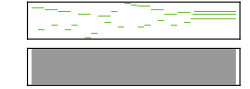

```mathematica
x=0.25;
Sound[{
SoundNote["C5",{1x,3x},"Harp",SoundVolume->0.75],
SoundNote["C3",{2x,3x},"Harp",SoundVolume->0.5],
SoundNote["Bb4",{3x,5x},"Harp",SoundVolume->0.75],
SoundNote["F3",{4x,5x},"Harp",SoundVolume->0.5],
SoundNote["Ab4",{5x,7x},"Harp",SoundVolume->0.75],
SoundNote["C3",{6x,7x},"Harp",SoundVolume->0.5],
SoundNote["F3",{7x,8x},"Harp",SoundVolume->0.5],
SoundNote["F4",{8x,10x},"Harp",SoundVolume->0.75],
SoundNote["Eb2",{9x,10x},"Harp",SoundVolume->0.5],
SoundNote["Ab2",{10x,11x},"Harp",SoundVolume->0.5],
SoundNote["Eb4",{11x,13x},"Harp",SoundVolume->0.75],
SoundNote["Ab3",{12x,13x},"Harp",SoundVolume->0.5],
SoundNote["Ab4",{13x,14x},"Harp",SoundVolume->0.75],
SoundNote["Eb3",{14x,15x},"Harp",SoundVolume->0.5],
SoundNote["F5",{15x,16x},"Harp",SoundVolume->0.75],
SoundNote["Eb5",{16x,17x},"Harp",SoundVolume->0.75],
SoundNote["D5",{17x,19x},"Harp",SoundVolume->0.75],SoundNote["Eb3",{17x,18x},"Harp",SoundVolume->0.5],
SoundNote["F3",{18x,19x},"Harp",SoundVolume->0.5],
SoundNote["Bb4",{19x,21x},"Harp",SoundVolume->0.75],
SoundNote["Bb3",{20x,21x},"Harp",SoundVolume->0.5],
SoundNote["F4",{21x,23x},"Harp",SoundVolume->0.75],
SoundNote["F3",{22x,23x},"Harp",SoundVolume->0.5],
SoundNote["G4",{23x,25x},"Harp",SoundVolume->0.75],
SoundNote["Ab3",{24x,25x},"Harp",SoundVolume->0.5],
SoundNote["C4",{25x,32x},"Harp",SoundVolume->0.75],SoundNote["F4",{25.25x,32x},"Harp",SoundVolume->0.75],SoundNote["Ab4",{25.5x,32x},"Harp",SoundVolume->0.75]}]
```

A slightly more advanced form of assigning time intervals is to add a constant to your time intervals. This isn't really necessary for the final product to work properly, but I like to use it because it makes writing the code much, much easier. Say your writing up your song and you've come far enough along that you don't want to have to listen to your entire song everytime you want to check new changes. You could simply open up a new blank notebook, write up the part of the song you're working on, and simply define the constant so that you can start the song at the time you're part plays. And when you're done, you can just copy and paste the new code onto the previous code.

For example, I've extracted the chorus to the Mathematica version of Bad Romance by Lady Gaga that I wrote up. The chorus starts around 70 seconds into the song, but as you can see, I've changed the time constant so that is starts at zero seconds in this notebook (expand code with bracket on right):

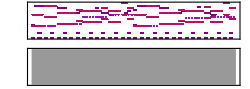

```mathematica
x=0.25;
b=-289x;
Sound[{
SoundNote["C3", {289 x + b, 289.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["BassDrum", {289 x + b, 290 x + b}], SoundNote[{"C3", "C4"}, {289 x + b, 293 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["CrashCymbal", {289 x + b, 290 x + b}],
SoundNote["C3", {290 x + b, 290.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {290 x + b, 291 x + b}, "Piano"],
SoundNote["C3", {291 x + b, 291.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {291 x + b, 292 x + b}, "Piano"], SoundNote["BassDrum", {291 x + b, 292 x + b}], SoundNote["ElectricSnare", {291 x + b, 292 x + b}],
SoundNote["C3", {292 x + b, 292.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {292 x + b, 293 x + b}, "Piano"],
SoundNote["C3", {293 x + b, 293.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {293 x + b, 294 x + b}, "Piano"], SoundNote["BassDrum", {293 x + b, 294 x + b}], SoundNote[{"A3", "A4"}, {293 x + b, 297 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["C3", {294 x + b, 294.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {294 x + b, 295 x + b}, "Piano"],
SoundNote["C3", {295 x + b, 295.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["BassDrum", {295 x + b, 296 x + b}], SoundNote["ElectricSnare", {295 x + b, 296 x + b}],
SoundNote["C3", {296 x + b, 296.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {296 x + b, 297 x + b}, "Piano"],
SoundNote["D3", {297 x + b, 297.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["G4", {297 x + b, 298 x + b}, "Piano"], SoundNote["BassDrum", {297 x + b, 298 x + b}], SoundNote[{"D3", "D4"}, {297 x + b, 303 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["D3", {298 x + b, 298.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["G4", {298 x + b, 299 x + b}, "Piano"],
SoundNote["D3", {299 x + b, 299.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["G4", {299 x + b, 300 x + b}, "Piano"], SoundNote["BassDrum", {299 x + b, 300 x + b}], SoundNote["ElectricSnare", {299 x + b, 300 x + b}],
SoundNote["D3", {300 x + b, 300.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["D4", {300 x + b, 302 x + b}, "Piano"],
SoundNote["D3", {301 x + b, 301.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["BassDrum", {301 x + b, 302 x + b}],
SoundNote["D3", {302 x + b, 302.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["D4", {302 x + b, 303 x + b}, "Piano"],
SoundNote["D3", {303 x + b, 303.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["D4", {303 x + b, 304 x + b}, "Piano"], SoundNote["BassDrum", {303 x + b, 304 x + b}], SoundNote["ElectricSnare", {303 x + b, 304 x + b}], SoundNote[{"F3", "F4"}, {303 x + b, 305 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["D3", {304 x + b, 304.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["E4", {304 x + b, 305 x + b}, "Piano"],

SoundNote["A3", {305 x + b, 305.5 x + b}, "Organ"], SoundNote["BassDrum", {305 x + b, 306 x + b}], SoundNote[{"E3", "E4"}, {305 x + b, 311 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["A3", {306 x + b, 306.5 x + b}, "Organ"], SoundNote["E4", {306 x + b, 307 x + b}, "Piano"],
SoundNote["A3", {307 x + b, 307.5 x + b}, "Organ"], SoundNote["E4", {307 x + b, 308 x + b}, "Piano"], SoundNote["BassDrum", {307 x + b, 308 x + b}], SoundNote["ElectricSnare", {307 x + b, 308 x + b}],
SoundNote["A3", {308 x + b, 308.5 x + b}, "Organ"], SoundNote["E4", {308 x + b, 309 x + b}, "Piano"],
SoundNote["A3", {309 x + b, 309.5 x + b}, "Organ"], SoundNote["G4", {309 x + b, 310 x + b}, "Piano"], SoundNote["BassDrum", {309 x + b, 310 x + b}],
SoundNote["A3", {310 x + b, 310.5 x + b}, "Organ"],
SoundNote["A3", {311 x + b, 311.5 x + b}, "Organ"], SoundNote["D4", {311 x + b, 312 x + b}, "Piano"], SoundNote[{"G3", "G4"}, {311 x + b, 313 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["BassDrum", {311 x + b, 312 x + b}], SoundNote["ElectricSnare", {311 x + b, 312 x + b}],
SoundNote["A3", {312 x + b, 312.5 x + b}, "Organ"], SoundNote["D4", {312 x + b, 313 x + b}, "Piano"],
SoundNote["C4", {313 x + b, 313.5 x + b}, "Organ"], SoundNote["C4", {313 x + b, 315 x + b}, "Piano"], SoundNote["BassDrum", {313 x + b, 314 x + b}], SoundNote[{"E3", "E4"}, {313 x + b, 317 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["C4", {314 x + b, 314.5 x + b}, "Organ"],
SoundNote["C4", {315 x + b, 315.5 x + b}, "Organ"], SoundNote["BassDrum", {315 x + b, 316 x + b}], SoundNote["ElectricSnare", {315 x + b, 316 x + b}],
SoundNote["C4", {316 x + b, 316.5 x + b}, "Organ"],
SoundNote["C4", {317 x + b, 317.5 x + b}, "Organ"], SoundNote["C4", {317 x + b, 318 x + b}, "Piano", SoundVolume -> 0.75], SoundNote[{"C4", "C5"}, {317 x + b, 319 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["BassDrum", {317 x + b, 318 x + b}],
SoundNote["C4", {318 x + b, 318.5 x + b}, "Organ"], SoundNote["D4", {318 x + b, 319 x + b}, "Piano", SoundVolume -> 0.75],
SoundNote["C4", {319 x + b, 319.5 x + b}, "Organ"], SoundNote["E4", {319 x + b, 320 x + b}, "Piano", SoundVolume -> 0.75], SoundNote[{"G3", "G4"}, {319 x + b, 321 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["BassDrum", {319 x + b, 320 x + b}], SoundNote["ElectricSnare", {319 x + b, 320 x + b}],
SoundNote["C4", {320 x + b, 320.5 x + b}, "Organ"], SoundNote["C4", {320 x + b, 321 x + b}, "Piano", SoundVolume -> 0.75],

SoundNote["C3", {321 x + b, 321.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["F4", {321 x + b, 322 x + b}, "Piano", SoundVolume -> 0.75], SoundNote["BassDrum", {321 x + b, 322 x + b}], SoundNote[{"C3", "C4"}, {321 x + b, 325 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["CrashCymbal", {321 x + b, 322 x + b}],
SoundNote["C3", {322 x + b, 322.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {322 x + b, 323 x + b}, "Piano"],
SoundNote["C3", {323 x + b, 323.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {323 x + b, 324 x + b}, "Piano"], SoundNote["BassDrum", {323 x + b, 324 x + b}], SoundNote["ElectricSnare", {323 x + b, 324 x + b}],
SoundNote["C3", {324 x + b, 324.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {324 x + b, 325 x + b}, "Piano"],
SoundNote["C3", {325 x + b, 325.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {325 x + b, 326 x + b}, "Piano"], SoundNote["BassDrum", {325 x + b, 326 x + b}], SoundNote[{"A3", "A4"}, {325 x + b, 329 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["C3", {326 x + b, 326.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {326 x + b, 327 x + b}, "Piano"],
SoundNote["C3", {327 x + b, 327.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {327 x + b, 328 x + b}, "Piano"], SoundNote["BassDrum", {327 x + b, 328 x + b}], SoundNote["ElectricSnare", {327 x + b, 328 x + b}],
SoundNote["C3", {328 x + b, 328.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["A4", {328 x + b, 329 x + b}, "Piano"],
SoundNote["D3", {329 x + b, 329.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["G4", {329 x + b, 330 x + b}, "Piano"], SoundNote["BassDrum", {329 x + b, 330 x + b}], SoundNote[{"D3", "D4"}, {329 x + b, 335 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["D3", {330 x + b, 330.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["G4", {330 x + b, 331 x + b}, "Piano"],
SoundNote["D3", {331 x + b, 331.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["G4", {331 x + b, 332 x + b}, "Piano"], SoundNote["BassDrum", {331 x + b, 332 x + b}], SoundNote["ElectricSnare", {331 x + b, 332 x + b}],
SoundNote["D3", {332 x + b, 332.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["D4", {332 x + b, 334 x + b}, "Piano"],
SoundNote["D3", {333 x + b, 333.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["BassDrum", {333 x + b, 334 x + b}],
SoundNote["D3", {334 x + b, 334.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["D4", {334 x + b, 335 x + b}, "Piano"],
SoundNote["D3", {335 x + b, 335.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["D4", {335 x + b, 336 x + b}, "Piano"], SoundNote["BassDrum", {335 x + b, 336 x + b}], SoundNote["ElectricSnare", {335 x + b, 336 x + b}], SoundNote[{"F3", "F4"}, {335 x + b, 337 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["D3", {336 x + b, 336.5 x + b}, "Organ", SoundVolume -> 2], SoundNote["E4", {336 x + b, 337 x + b}, "Piano"],

SoundNote["G#3", {337 x + b, 337.5 x + b}, "Organ"], SoundNote["BassDrum", {337 x + b, 338 x + b}], SoundNote[{"E3", "E4"}, {337 x + b, 343 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["G#3", {338 x + b, 338.5 x + b}, "Organ"], SoundNote["E4", {338 x + b, 339 x + b}, "Piano"],
SoundNote["G#3", {339 x + b, 339.5 x + b}, "Organ"], SoundNote["E4", {339 x + b, 340 x + b}, "Piano"], SoundNote["BassDrum", {339 x + b, 340 x + b}], SoundNote["ElectricSnare", {339 x + b, 340 x + b}],
SoundNote["G#3", {340 x + b, 340.5 x + b}, "Organ"], SoundNote["E4", {340 x + b, 341 x + b}, "Piano"],
SoundNote["G#3", {341 x + b, 341.5 x + b}, "Organ"], SoundNote["G#4", {341 x + b, 342 x + b}, "Piano"], SoundNote["BassDrum", {341 x + b, 342 x + b}],
SoundNote["G#3", {342 x + b, 342.5 x + b}, "Organ"],
SoundNote["G#3", {343 x + b, 343.5 x + b}, "Organ"], SoundNote["D4", {343 x + b, 344 x + b}, "Piano"], SoundNote[{"G#3", "G#4"}, {343 x + b, 345 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["BassDrum", {343 x + b, 344 x + b}], SoundNote["ElectricSnare", {343 x + b, 344 x + b}],
SoundNote["G#3", {344 x + b, 344.5 x + b}, "Organ"], SoundNote["D4", {344 x + b, 345 x + b}, "Piano"],
SoundNote["A3", {345 x + b, 345.5 x + b}, "Organ"], SoundNote["C4", {345 x + b, 347 x + b}, "Piano"], SoundNote["BassDrum", {345 x + b, 346 x + b}], SoundNote[{"E3", "E4"}, {345 x + b, 349 x + b}, "Strings", SoundVolume -> 0.6],
SoundNote["A3", {346 x + b, 346.5 x + b}, "Organ"],
SoundNote["A3", {347 x + b, 347.5 x + b}, "Organ"], SoundNote["BassDrum", {347 x + b, 348 x + b}], SoundNote["ElectricSnare", {347 x + b, 348 x + b}],
SoundNote["A3", {348 x + b, 348.5 x + b}, "Organ"],
SoundNote["A3", {349 x + b, 349.5 x + b}, "Organ"],SoundNote[{"C4", "C5"}, {349 x + b, 351 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["BassDrum", {349 x + b, 350 x + b}],
SoundNote["A3", {350 x + b, 350.5 x + b}, "Organ"], 
SoundNote["A3", {351 x + b, 351.5 x + b}, "Organ"], SoundNote[{"G3", "G4"}, {351 x + b, 353 x + b}, "Strings", SoundVolume -> 0.6], SoundNote["BassDrum", {351 x + b, 352 x + b}], SoundNote["ElectricSnare", {351 x + b, 352 x + b}],
SoundNote["A3", {352 x + b, 352.5 x + b}, "Organ"]
}]
```

### Copy, Paste, Find, Replace

Probably the most obvious way to speed up writing up a song is to copy/paste your old parts and change the times and modify them as needed to create new parts. Since songs tend to repeat parts a lot, you'll definitely be doing this a lot. When I was writing up my Lady Gaga songs, I'd say roughly 60-70% of the time was spent changing the time intervals of the repeating phrases after pasting them onto the existing piece. However, I didn't discover until late in the game (Telephone, actually) that there is a much faster, easier, and almost error-free way of doing this. Use Command-F or Control-F to open the FIND window. Here you can look up strings of letters or words within the notebook you're working in. You also have the option to replace the strings you find with different strings. You can probably already see how this would make things so much faster, especially with the REPLACE ALL option.

Let's say I wanted to copy/paste this familiar tune to another part of the song:

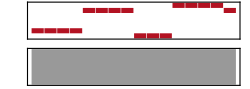

```mathematica
x=0.25;
b=-33x;
Sound[{
SoundNote["E4",{33x+b,34x+b},"Polysynth"],
SoundNote["E4",{34x+b,35x+b},"Polysynth"],
SoundNote["E4",{35x+b,36x+b},"Polysynth"],
SoundNote["E4",{36x+b,37x+b},"Polysynth"],
SoundNote["G#4",{37x+b,38x+b},"Polysynth"],
SoundNote["G#4",{38x+b,39x+b},"Polysynth"],
SoundNote["G#4",{39x+b,40x+b},"Polysynth"],
SoundNote["G#4",{40x+b,41x+b},"Polysynth"],
SoundNote["D#4",{41x+b,42x+b},"Polysynth"],
SoundNote["D#4",{42x+b,43x+b},"Polysynth"],
SoundNote["D#4",{43x+b,44x+b},"Polysynth"],
SoundNote["A4",{44x+b,45x+b},"Polysynth"],
SoundNote["A4",{45x+b,46x+b},"Polysynth"],
SoundNote["A4",{46x+b,47x+b},"Polysynth"],
SoundNote["A4",{47x+b,48x+b},"Polysynth"],
SoundNote["G#4",{48x+b,49x+b},"Polysynth"]}]
```

I would then open it up in its own notebook, open the find window, and do the following:

And now, I have the exact same tune, but plays eight seconds later in the song.

```mathematica
x=0.25;
b=-65x;
Sound[{
SoundNote["E4",{65x+b,66x+b},"Polysynth"],
SoundNote["E4",{66x+b,67x+b},"Polysynth"],
SoundNote["E4",{67x+b,68x+b},"Polysynth"],
SoundNote["E4",{68x+b,69x+b},"Polysynth"],
SoundNote["G#4",{69x+b,70x+b},"Polysynth"],
SoundNote["G#4",{70x+b,71x+b},"Polysynth"],
SoundNote["G#4",{71x+b,72x+b},"Polysynth"],
SoundNote["G#4",{72x+b,73x+b},"Polysynth"],
SoundNote["D#4",{73x+b,74x+b},"Polysynth"],
SoundNote["D#4",{74x+b,75x+b},"Polysynth"],
SoundNote["D#4",{75x+b,76x+b},"Polysynth"],
SoundNote["A4",{76x+b,77x+b},"Polysynth"],
SoundNote["A4",{77x+b,78x+b},"Polysynth"],
SoundNote["A4",{78x+b,79x+b},"Polysynth"],
SoundNote["A4",{79x+b,80x+b},"Polysynth"],
SoundNote["G#4",{80x+b,81x+b},"Polysynth"]}]
```

-Graphics-

## Common Errors and Tips for Troubleshooting

Writing songs in Mathematica can be really fun and entertaining, but at the same time can be really frustrating, especially when things go wrong! Here are some things you might run into and my advice for the steps you should take in order to fix them.

### Syntax

Every once and awhile, you'll compile you're code and Mathematica will just spit back all of your input without creating a sound player. This is because somewhere in your code, you wrote something wrong or accidentally left some punctuation somewhere where you meant to take it out and forgot. Most of the time when I get this error, it's because I left a comma at the end of my code. You can easily tell this if the word "Null" appears at the end of the spit-out.

However, sometimes these errors are less obvious. Let's say I was going along and accidentally deleted a comma somewhere in my code, but I didn't know the cause of my error or where to look. How would I find it? Well, like any other programmer, you would probably use comments to eliminate possible lines that contain the error. Add comments to the end and middle of you code and change the location of the first comment bracket and compile until you are able to find the boundary between where your code works and doesn't work. Then you should without a doubt be able to locate your error, it just may take some time. Note: be sure to put your comment brackets in code in places where they will not disrupt your syntax. Then you'll never find your error because you will always get syntax errors.

### Song Writing Errors

Well, what if it's not necessarily the syntax that I'm screwing up, but the actual notes themselves? How do I make the song sound the way I want it too? Well, you can use a lot of the same techniques as above, such as commenting things out. Except the twist here is it's not so obvious when you've come across you're error because you're code will still produce a song you can listen to. This takes a bit of skill. The sound player shows you the notes of the song in the order they play in the song from left to right, with the relative heights representing different pitches. Longer lines represent longer notes and the different colors represent different instruments. Looking at the final product of songs with multiple instruments can be a bit confusing, but as you add more and more instruments to your own songs, you'll naturally be able to distinguish the different colors of the instruments and what the shapes of the notes should look like. If you organize your code effectively, you should be able to narrow down where you errors are based on listening and viewing the sound player. You may need to only view a small amount of your code at one time in order to do this, but it's worth it because I know from experience that this can be a long and difficult process. But with practice, you'll get more efficient at doing this.

## Other Fun Tidbits

When you're done with your piece, don't forget to make you're Mathematica notebook beautiful. You can add some images by just going to Insert -> Picture -> From File. It's not difficult to do, not to mention somewhat fun.